# Shooting the Sun

Consider a two-body solar system with just the Sun and and the Earth (see figure). Assume the Earth (mass M_E) and the Sun (mass M_S) follow circular orbits around the center of mass of the Earth-Sun system. The Earth-Sun distance is R_E=L_S + L_E. The origin is placed at the center of mass (CM) and at t=0 the Earth and Sun are in the configuration shown in the figure. A projectile (mass m_p) is launched from the Earth at t=0 with a mass much, much smaller than the mass of the Earth or the Sun. It has velocity v_0 relative to the moving Earth and is launched at the angle ϕ as shown in the figure.

## 1. Making a Model.

The trajectory of a projectile launched from the Earth in our simplified solar system will be determined solely be the Earth’s and the Sun’s gravity or

(F⃗)_p= -G(M_S m_p)/r_Sp^2(r̂)_Sp - G(M_E m_p)/r_Ep^2(r̂)_Ep

where M_S and M_E are the Sun and Earth masses respectively, m_p is the projectile mass, r_Sp and r_Ep are respectively the distances from the projectile to the Sun and Earth, and (r̂)_Sp and (r̂)_Ep are unit vectors pointing in the direction of the gravitational forces acting on the projectile. Assume the projectile is launched from a point on the surface of the Earth pointed radially outward at the angle ϕ as shown in the figure and that the Earth and Sun follow circular orbits around their mutual center of mass. You should show that the x and y components of the projectile’s motion are governed by the following equations.

(d^2 x)/dt^2= -GM_S/r_Sp^3(x_p + L_S cosωt)  -GM_E/r_Ep^3(x_p - L_E cosωt) 


(d^2 y)/dt^2= -GM_S/r_Sp^3(y_p + L_S sinωt)  -GM_E/r_Ep^3(y_p - L_E sinωt)

## 2. Solving the Equation

Write a code that will solve the model of the projectile in the Earth-Sun solar system from Section 1. Calculate the trajectory for the following initial conditions and parameters to compare your results with others. The escape velocity of the Earth is v_escape.

t_0 = 0.0 s                ϕ = 25^O              v_0 = 1.5 v_escape

M_S= 1.99×10^30 kg
M_E= 5.97×10^24 kg
R_E= 1.5×10^11 m
r_E= 6.37×10^6 m
r_S= 6.96×10^8 m
v_escape = 1.1×10^4 m/s

Integration step size: 1000 s    Time Limit: 3 years (*convert to seconds*)

## 3. Testing the Code

Test your code by generating a plot of trajectory for some ‘simple’ initial conditions, i.e.  for circular motion, around the Sun.  Turn off the gravity exerted by the Earth to test the trajectory  (set the mass of Earth and the angular velocity of earth to zero).  Set the velocity of the projectile to the its orbital velocity around the sun a distance RE  away.

## 4. Investigating the Physics

Once you have a working code consider the following. You are chair of the government committee assessing the feasibility of using railguns to shoot canisters of nuclear waste into the Sun. You want to map out the necessary conditions for doing this, namely the initial speed and directions of the canisters that will end up crashing into the Sun. Generate a plot of initial velocity v_0 and angle ϕ showing where the waste canisters will be in three years after launch. To do this use a Monte Carlo technique to generate a distribution in v_0-ϕ space and choose different colors for the final projectile-CM distance at each v_0-ϕ  point. The result of your calculation should be an array with each element containing the initial angle ϕ, the initial velocity,  and the final distance of the projectile from the center of mass. To make the plot, see Part 6 below for a new command that will take the output and construct the phase space portrait. Once you have the v_0-ϕ distribution, consider the following questions.

1. What launch speeds are required? How do they compare with existing launch methods?

2. What accuracy is required in the launch angle to hit the Sun?

3. Regardless of cost,  is shooting nuclear waste canisters into the Sun a viable disposal method? 

4. What questions need more study? What is your recommendation?

## 5. Some Necessary Commands.

A convenient technique when making long, complex calculations is to create a new function that encodes the entire calculation. The codes below show how to turn a multi-step calculation into a single function. The calculation also demonstrates the use of a While loop and the Break[] command used to exit a loop. The Break[] command will be useful when your projectile crashes into the Earth or the Sun.

First study the code before making it a function. See what happens to the length of the output array path if you lower fnLimit.

```mathematica
a0=2.0;
b0=0.2;
time=0;
timeLimit=100;
timeStep=0.01;
fnLimit=1000;
path={};
While[time< timeLimit,
fn = a0*time + b0*time^2;
AppendTo[path,{time,fn}];
If[fn>fnLimit, Break[]];
time = time+ timeStep;
] (* end of While loop. *)
Length[path]
```

The code below now defines a funtion that performs the same task as in the cell above where fnLimit is now the argument of the function test and the output is the last item in the function which is the length of the path array.

```mathematica
test[fnLimit_] := {
a0=2.0;
b0=0.2;
time=0;
timeLimit=100;
timeStep=0.01;
path={};
While[time< timeLimit,
fn = a0*time + b0*time^2;
AppendTo[path,{time,fn}];
If[fn>fnLimit, Break[]];
time = time+ timeStep;
]; (* end of While loop. *)
Length[path]
} (* end of function definition. *)
```

```mathematica
test[120.0]
```

## 6. Plotting Your Results.

Once you have obtained the data to plot the grid use the following command to make that plot. The assumptions that go into the code below are that (1) the input file is made of rows with three columns consisting of initial ϕ and v_0 and the final distance from the CM of the Earth-Moon system, (2) an entry in column three of ‘-2’ means the projectile hit the Earth, and (3) an entry of ‘-1’ means the projectile struck the Sun.  
First plot the data you generated above. t1 will equal your table of data instead of reading in a file
Then copy the threeBodyTest.dat to the desktop, read in, and plot the data. (you will need to change the directory name where the file is being read from)

```mathematica
(* Read in the data (phi, v0, dC) and measure some properties for the plot. 
On Linux the read command might look like the following.
 t1 = ReadList["/media/flash/215s12/examples/3body/threeBodyTest.dat",{Number,Number,Number}]; *)
(* On Windows the read command might look like the following. Put your path in. *)
t1 = ReadList["C:\\Users\\Omair\\Desktop\\threeBodyTest.dat",{Number,Number,Number}];
myNmax=Length[t1];
mymin=1*10^75;
i=1;
While[i<myNmax,
If[ t1[[i,3]]<mymin,If[t1[[i,3]]>0,mymin=t1[[i,3]]]];
i=i+1]
mymax=Max[Table[t1[[i,3]],{i,1,myNmax}]];
range=mymax-mymin;
(* Make the final table with the color code for the final distance as the last element. *)
t2=Table[
{t1[[i,1]],
t1[[i,2]],
If[t1[[i,3]]<0,If[t1[[i,3]]==-1,0.9,0.7],0.25*(1-((t1[[i,3]]-mymin)/range))]},{i,1,myNmax}
];
```

The code below defines a new function ThreeBodyScatterPlot used to plot the results of the calculation and shows its usage.  You do not need to completely understand this function but know that it only plots data with from an array with 3 values for each data point.

```mathematica
(* Define the plotting function. Underscore means hold value until defined *)
ThreeBodyScatterPlot[data_/;
   MatrixQ[data, NumberQ] &&  (* Matrix Q elvaluates true if data is an array AND has 3 numbers in a data set *)
   Length[First[data]] === 3,fun_, opts___] :=  
   Show[Graphics[
          {PointSize[0.005],
           Map[{fun[Last[#]],Point[Take[#, 2]]}&, data]
          }, opts
        ]
 ]
```

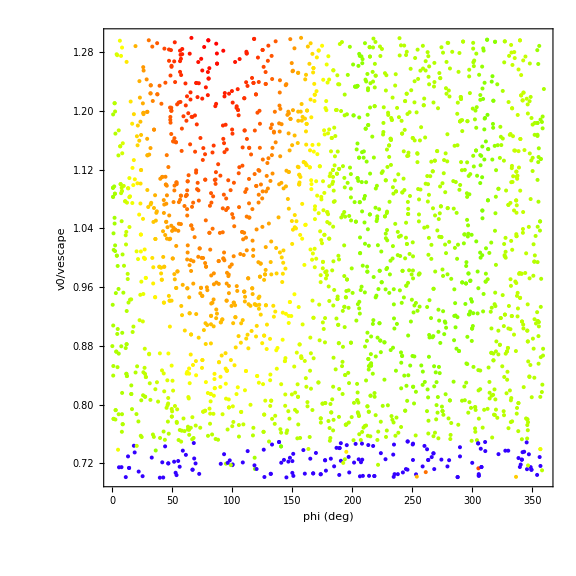

```mathematica
(* Make the plot. *)
p5=ThreeBodyScatterPlot[t2,
              Hue[#,1,If[#==0.9,0,1]]&,         (* applies color according to hitting the sun, earth or inbetween *)
              Axes->True,
              AxesLabel->{"x","y","z"},
              AspectRatio->1,
              Frame->True,
              PlotRange->{ {0,360},
                           {0.7,1.3}},
              BaseStyle->FontSize->16,
              ImageSize->8*72,
              Frame->True,
              FrameLabel->{"phi (deg)","v0/vescape"}
             ]
```

Place graph from 3 and 6 into chelms netfiles